```mathematica
piNot[Np_,lambda_,nu_ ] := 1/(1  + Sum[Product[((Np - (j-1))*nu)/(lambda*j),{j,i}]   ,{i,Np}])
```

```mathematica
piNot[5,0.2,0.2]
```

0.03125

```mathematica
N[72/27069869]
```

2.65978×10^-6

```mathematica
piI[Np_, lambda_, nu_, index_] := Product[((Np - (j-1))*nu)/(lambda*j),{j,index}]*piNot[Np,lambda,nu]
```

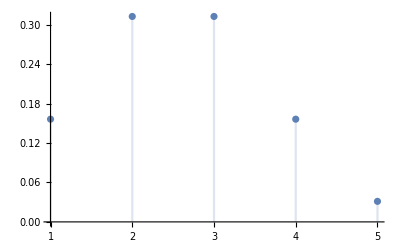

```mathematica
DiscretePlot[piI[5,0.2,0.2, i],{i,5}]
```

```mathematica
5
```

```mathematica
pAvg[Np_,lambda_,nu_ ] := Sum[piI[Np, lambda, nu, index] * index, {index, Np}]
```

```mathematica
piI[10,0.3,0.4,2]
```

0.0167233

0.03125 Abs[((-1.)^i Pochhammer[-5.,i])/Pochhammer[1.,i]]

```mathematica
pAvg[5,0.2,0.2]
```

2.5

```mathematica
RateTown[N_,Nt_, lambda_,nu_, L_] := Nt * (1 -  (Nt + pAvg[(N - Nt), lambda, nu])/L)
```

```mathematica
RateCity[N_,Nt_, lambda_,nu_, L_] := pAvg[(N - Nt), lambda, nu] * (1- (N - Nt - pAvg[(N - Nt), lambda, nu])/L)
```

```mathematica
ListLinePlot[Table[{RateTown[10,Nt,0.2,0.05, 30],RateCity[N1,Nt,0.2,0.05, 30]},{Nt, 1,N,1}] ], {N1,2,10,1}]
```

```mathematica
pAvg[0,0.2,0.2]
```

0

```mathematica
Table[{RateTown[10,Nt,0.2,0.05, 10],RateCity[10,Nt,0.2,0.05, 10]},{Nt, 1,10,1}]
```

{{0.72,0.504},{1.28,0.576},{1.68,0.616},{1.92,0.624},{2.,0.6},{1.92,0.544},{1.68,0.456},{1.28,0.336},{0.72,0.184},{0,0}}

```mathematica
RateTown[10,10,0.2,0.05,10]
```

0